# Geometria

## Geometria plana

Gerar formatos em 2D:



```mathematica
Graphics[Disk[]]
```

Use diretivas para combinar gráficos e mudar seus estilos:



```mathematica
Graphics[{Red, Disk[]}]
```

Objetos geométricos consideram listas como coordenadas:

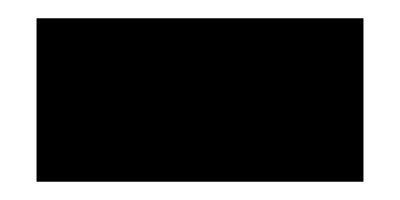

```mathematica
Graphics[Rectangle[{0, 0}, {4, 2}]]
```

## Triângulos

Gerar triângulos com comandos como SASTriangle:

```mathematica
tr = SASTriangle[1, 90 °, 2]
```

Triangle[{{0,0},{√5,0},{4/(√5),2/(√5)}}]

Use Graphics para obter uma representação gráfica:

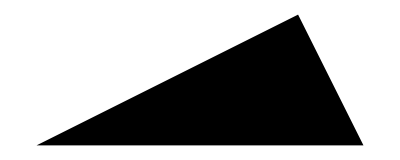

```mathematica
Graphics[tr]
```

Propriedades como área podem ser calculadas diretamente:

```mathematica
Area[tr]
```

1

## Sólidos geométricos

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

Calcule o volume e outras propriedades:

```mathematica
Volume[Cylinder[]]
```

2 π

Encontrar fórmulas e outras informações com linguagem natural:

volume of a cone

Function[{a,h},1/3 h π a^2]

## Transformações geométricas

Rotate:


{-Graphics-,-Graphics-}

```mathematica
{
Graphics[Rectangle[]],
Graphics[Rotate[Rectangle[], 45 °]]
}
```

Translate:

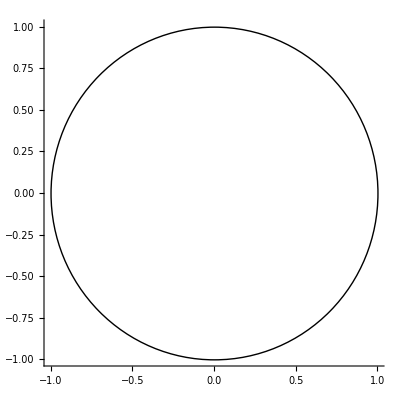
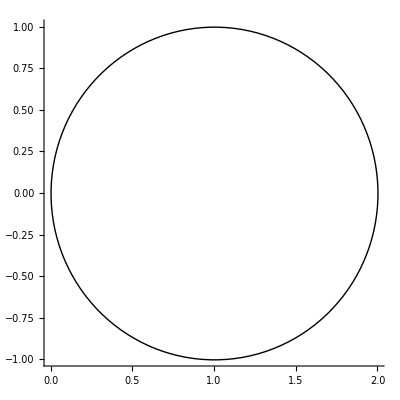

```mathematica
{
Graphics[Circle[], Axes -> True],
Graphics[Translate[Circle[], {1, 0}], Axes -> True]
}
```

Scale:

```mathematica
{
Graphics[Disk[]],
Graphics[ Scale[Disk[], {1, 1/2}]]
}
```

{-Graphics-,-Graphics-}